### Overview/summary

I have six wells corresponding to six different electroporation protocols. I calculated the efficiency and cell viability for each method. Efficiency is the number of GFP+ cells over total number of live cells. Cell viability is the number of dead cells over the number of total cells. 

Efficiency: absolute number, percentage of positive (> 1500), and total number live cells for post medium change with Sytox Red:

```mathematica
{Map[Function[gfpIntensity,Length[Select[gfpIntensity[[1]],#>1500&]]//N],{gfpIntensitiesWell1, gfpIntensitiesWell2, gfpIntensitiesWell3, gfpIntensitiesWell4, gfpIntensitiesWell5, gfpIntensitiesWell6}],Map[Function[gfpIntensity,Length[Select[gfpIntensity[[1]],#>1500&]]/Length[gfpIntensity[[1]]]//N],{gfpIntensitiesWell1, gfpIntensitiesWell2, gfpIntensitiesWell3, gfpIntensitiesWell4, gfpIntensitiesWell5, gfpIntensitiesWell6}], Map[Function[gfpIntensity,Length[gfpIntensity[[1]]]//N],{gfpIntensitiesWell1, gfpIntensitiesWell2, gfpIntensitiesWell3, gfpIntensitiesWell4, gfpIntensitiesWell5, gfpIntensitiesWell6}]}
```

{{586.,1017.,2331.,874.,1182.,764.},{0.573947,0.62739,0.536602,0.54252,0.538742,0.60443},{1021.,1621.,4344.,1611.,2194.,1264.}}

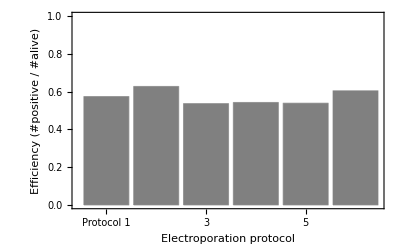

```mathematica
BarChart[{0.5739471106758081,0.6273904996915485,0.5366022099447514,0.54252017380509,0.5387420237010028,0.6044303797468354},ChartLabels->{"Protocol 1", "2", "3", "4", "5", "6"}, Frame -> True, PlotRange->{All, {0,1}}, FrameLabel->{"Electroporation protocol", "Efficiency (#positive / #alive)"}, ChartStyle->Gray]
```

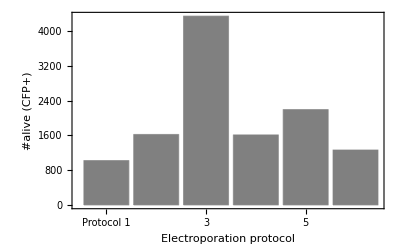

```mathematica
BarChart[{1021.,1621.,4344.,1611.,2194.,1264.},ChartLabels->{"Protocol 1", "2", "3", "4", "5", "6"}, Frame -> True, PlotRange->{All, All}, FrameLabel->{"Electroporation protocol", "#alive (CFP+)"}, ChartStyle->Gray]
```

Well 3 has a similar percentage efficiency as the rest, but much greater live cell number.

Number of dead cells detected in each file, broken up into groups of time points:

(2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy1c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy2c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy3c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy4c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy5c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy6c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy1c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy2c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy3c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy4c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy5c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy6c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy1c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy2c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy3c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy4c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy5c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy6c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy1c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy2c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy3c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy4c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy5c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy6c4_table.csv)

```mathematica
Partition[deadResultsLists[[;;,-1,1]],6]
```

{{0,83,72,97,97,83},{0,117,141,140,109,33},{197,3099,1697,2497,3416,2007},{2428,5380,3158,4034,4142,3975}}

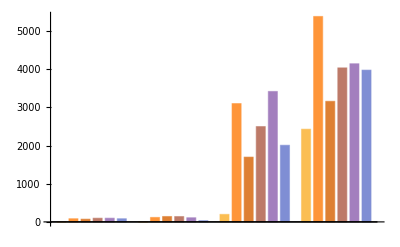

```mathematica
BarChart[Partition[deadResultsLists[[;;,-1,1]],6]]
```

Viability: number of live cells divided by number of live + dead cells:

```mathematica
{1021.,1621.,4344.,1611.,2194.,1264.}/({1021.,1621.,4344.,1611.,2194.,1264.}+{2428,5380,3158,4034,4142,3975})
```

{0.296028,0.231538,0.579046,0.285385,0.346275,0.241267}

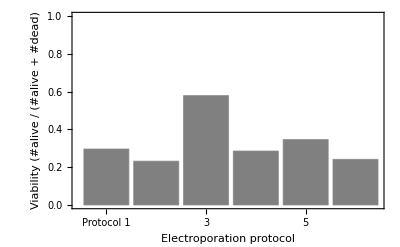

```mathematica
BarChart[{0.2960278341548275,0.23153835166404801,0.5790455878432418,0.2853852967227635,0.34627525252525254,0.2412674174460775},ChartLabels->{"Protocol 1", "2", "3", "4", "5", "6"}, Frame -> True, PlotRange->{All, {0,1}}, FrameLabel->{"Electroporation protocol", "Viability (#alive / (#alive + #dead)"}, ChartStyle->Gray]
```

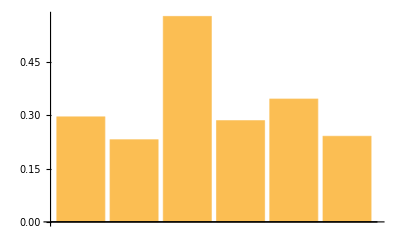

```mathematica
BarChart[{0.2960278341548275,0.23153835166404801,0.5790455878432418,0.2853852967227635,0.34627525252525254,0.2412674174460775}]
```

Well three seems to have highest viability at ~58%.

```mathematica
4344/(4344+3158)//N
```

0.579046

### Efficiency

#### Setup

```mathematica
SetOptions[Histogram,BaseStyle->{FontFamily->"Arial",FontSize->14}];
SetOptions[BarChart,BaseStyle->{FontFamily->"Arial",FontSize->14}];
resultsDirectory="Z:\\results\\2017_12_15_expt_16\\2018_01_05_ilastik_live_cell_results";
resultsFiles=FileNames["*.csv",resultsDirectory];
Map[FileNameTake,resultsFiles]//MatrixForm
SetOptions[EvaluationNotebook[],ImageSizeMultipliers->{1,1}]
```

(2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_c1_c3_table.csv
2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1_c1_c3_table.csv
2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_2_c1_c3_table.csv
2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3_c1_c3_table.csv
2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_4_c1_c3_table.csv
2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_5_c1_c3_table.csv
2018_01_05_ilastik_live_cell_results-JC_171215_expt016_pre_medium_change_c1_c3_table.csv
2018_01_05_ilastik_live_cell_results-JC_171215_expt016_pre_medium_change_SytR_c1_c3_table.csv)

```mathematica
resultsLookupAssociation=AssociationThread[Map[FileNameTake,resultsFiles],Range[Length[resultsFiles]]]
```

<|2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_c1_c3_table.csv→1,2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1_c1_c3_table.csv→2,2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_2_c1_c3_table.csv→3,2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3_c1_c3_table.csv→4,2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_4_c1_c3_table.csv→5,2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_5_c1_c3_table.csv→6,2018_01_05_ilastik_live_cell_results-JC_171215_expt016_pre_medium_change_c1_c3_table.csv→7,2018_01_05_ilastik_live_cell_results-JC_171215_expt016_pre_medium_change_SytR_c1_c3_table.csv→8|>

```mathematica
resultsLists = Map[Import[#]&,resultsFiles];
```

```mathematica
resultsLists[[resultsLookupAssociation["2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_c1_c3_table.csv"]]]
```

{1}
 |  |  |  |

```mathematica
resultsLists
```

{1}
 |  |  |  |

#### Well 2

Get list of GFP intensities for well #2 from the dataset (csv counting starts from 0):

```mathematica
gfpIntensitiesPreMediumChange=Select[resultsLists[[resultsLookupAssociation["2018_01_05_ilastik_live_cell_results-JC_171215_expt016_pre_medium_change_c1_c3_table.csv"]]],#[[2]]==1&][[;;,10]];gfpIntensitiesPostMediumChange=Select[resultsLists[[resultsLookupAssociation["2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_c1_c3_table.csv"]]],#[[2]]==1&][[;;,10]];gfpIntensitiesPostMediumChangeDay1=Select[resultsLists[[resultsLookupAssociation["2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1_c1_c3_table.csv"]]],#[[2]]==1&][[;;,10]];
```

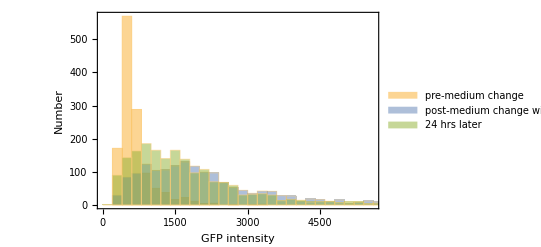

```mathematica
Histogram[{gfpIntensitiesPreMediumChange,gfpIntensitiesPostMediumChange,gfpIntensitiesPostMediumChangeDay1}, Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"pre-medium change", "post-medium change with Sytox Red", "24 hrs later"}]
```

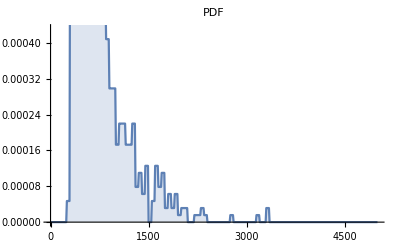
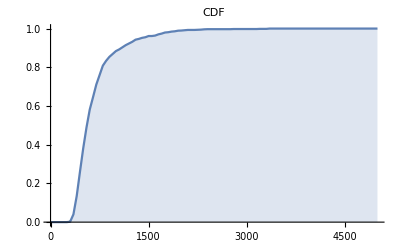

```mathematica
𝒟=HistogramDistribution[gfpIntensitiesPreMediumChange];
DiscretePlot[#[𝒟,x],{x,0,5000,10},PlotLabel->#]&/@{PDF,CDF}
```

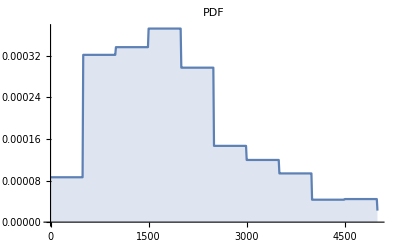
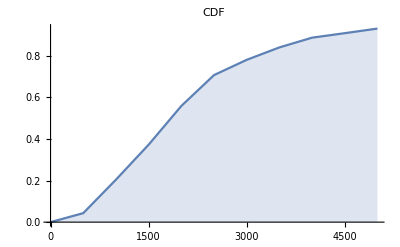

```mathematica
𝒟=HistogramDistribution[gfpIntensitiesPostMediumChange];
DiscretePlot[#[𝒟,x],{x,0,5000,10},PlotLabel->#]&/@{PDF,CDF}
```

Looking at this, let’s arbitrarily say that intensity > 1000 is positive. Then the percentage positive would be about 80%

```mathematica
Length[Select[gfpIntensitiesPreMediumChange,#>1000&]]/Length[gfpIntensitiesPreMediumChange]//N
```

0.116261

```mathematica
Length[Select[gfpIntensitiesPostMediumChange,#>1000&]]/Length[gfpIntensitiesPostMediumChange]//N
```

0.795805

#### All wells

```mathematica
({{"2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_c1_c3_table.csv"}, {"2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1_c1_c3_table.csv"}, {"2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_2_c1_c3_table.csv"}, {"2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3_c1_c3_table.csv"}, {"2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_4_c1_c3_table.csv"}, {"2018_01_05_ilastik_live_cell_results-JC_171215_expt016_post_medium_change_SytR_day_5_c1_c3_table.csv"}, {"2018_01_05_ilastik_live_cell_results-JC_171215_expt016_pre_medium_change_c1_c3_table.csv"}, {"2018_01_05_ilastik_live_cell_results-JC_171215_expt016_pre_medium_change_SytR_c1_c3_table.csv"}})
```

```mathematica
gfpIntensitiesWell1=Map[Function[resultsList, Select[resultsList,#[[2]]==0&][[;;,10]]],resultsLists];
gfpIntensitiesWell2=Map[Function[resultsList, Select[resultsList,#[[2]]==1&][[;;,10]]],resultsLists];
gfpIntensitiesWell3=Map[Function[resultsList, Select[resultsList,#[[2]]==2&][[;;,10]]],resultsLists];
gfpIntensitiesWell4=Map[Function[resultsList, Select[resultsList,#[[2]]==3&][[;;,10]]],resultsLists];
gfpIntensitiesWell5=Map[Function[resultsList, Select[resultsList,#[[2]]==4&][[;;,10]]],resultsLists];
gfpIntensitiesWell6=Map[Function[resultsList, Select[resultsList,#[[2]]==5&][[;;,10]]],resultsLists];
```

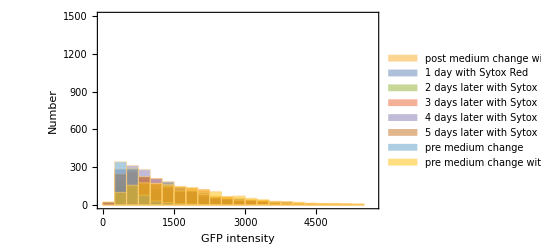
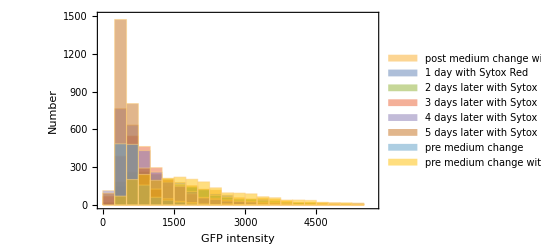
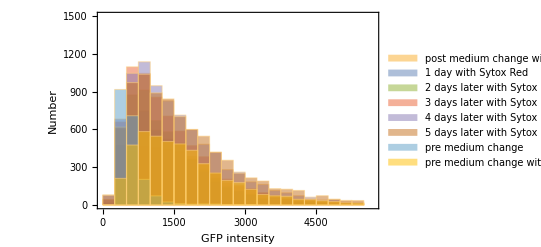
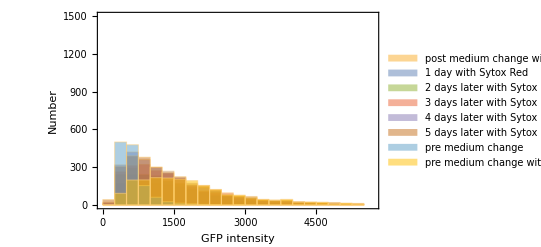
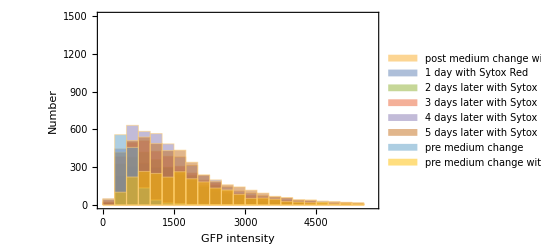
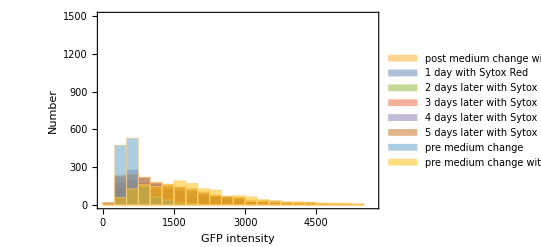

```mathematica
{Histogram[Table[gfpIntensitiesWell1[[i]],{i,Length[gfpIntensitiesWell1]}], {0,5500,250},Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}, PlotRange->{{0,5700},{0,1500}}],
Histogram[Table[gfpIntensitiesWell2[[i]],{i,Length[gfpIntensitiesWell2]}],  {0,5500,250},Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}, PlotRange->{{0,5700},{0,1500}}],
Histogram[Table[gfpIntensitiesWell3[[i]],{i,Length[gfpIntensitiesWell3]}],  {0,5500,250},Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}, PlotRange->{{0,5700},{0,1500}}],
Histogram[Table[gfpIntensitiesWell4[[i]],{i,Length[gfpIntensitiesWell4]}], {0,5500,250}, Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}, PlotRange->{{0,5700},{0,1500}}],
Histogram[Table[gfpIntensitiesWell5[[i]],{i,Length[gfpIntensitiesWell5]}], {0,5500,250}, Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}, PlotRange->{{0,5700},{0,1500}}],Histogram[Table[gfpIntensitiesWell6[[i]],{i,Length[gfpIntensitiesWell6]}], {0,5500,250},Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}, PlotRange->{{0,5700},{0,1500}}]}
```

Plot fewer times:

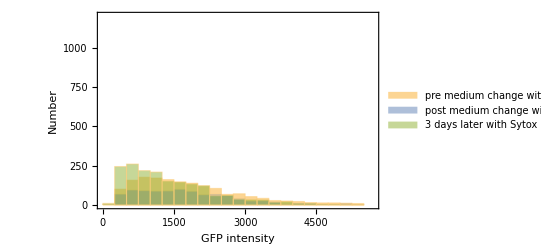
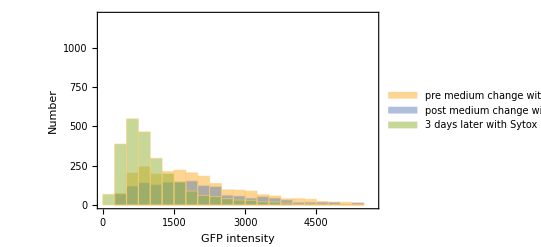
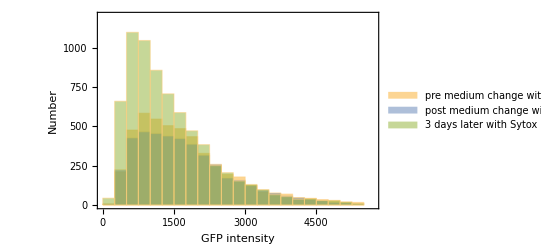
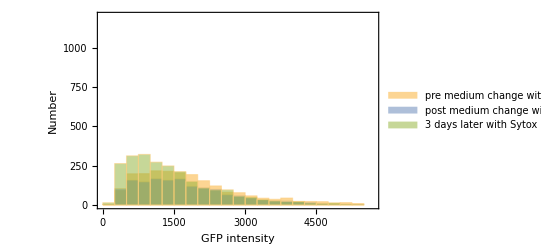
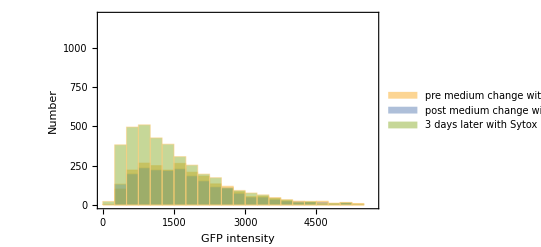
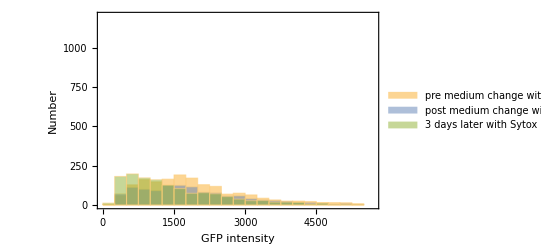

```mathematica
{Histogram[Table[gfpIntensitiesWell1[[i]],{i,{8,1,4}}], {0,5500,250},Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"pre medium change with Sytox Red","post medium change with Sytox Red", "3 days later with Sytox Red"}, PlotRange->{{0,5700},{0,1200}}],
Histogram[Table[gfpIntensitiesWell2[[i]],{i,{8,1,4}}],  {0,5500,250},Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"pre medium change with Sytox Red","post medium change with Sytox Red", "3 days later with Sytox Red"}, PlotRange->{{0,5700},{0,1200}}],
Histogram[Table[gfpIntensitiesWell3[[i]],{i,{8,1,4}}],  {0,5500,250},Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"pre medium change with Sytox Red","post medium change with Sytox Red", "3 days later with Sytox Red"}, PlotRange->{{0,5700},{0,1200}}],
Histogram[Table[gfpIntensitiesWell4[[i]],{i,{8,1,4}}], {0,5500,250}, Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"pre medium change with Sytox Red","post medium change with Sytox Red", "3 days later with Sytox Red"}, PlotRange->{{0,5700},{0,1200}}],
Histogram[Table[gfpIntensitiesWell5[[i]],{i,{8,1,4}}], {0,5500,250}, Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"pre medium change with Sytox Red","post medium change with Sytox Red", "3 days later with Sytox Red"}, PlotRange->{{0,5700},{0,1200}}],Histogram[Table[gfpIntensitiesWell6[[i]],{i,{8,1,4}}], {0,5500,250},Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"pre medium change with Sytox Red","post medium change with Sytox Red", "3 days later with Sytox Red"}, PlotRange->{{0,5700},{0,1200}}]}
```

Plotting the CDF:

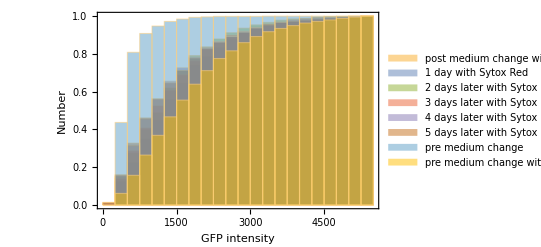
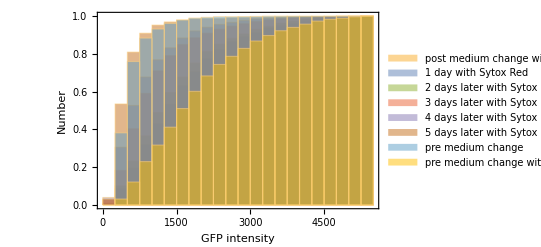
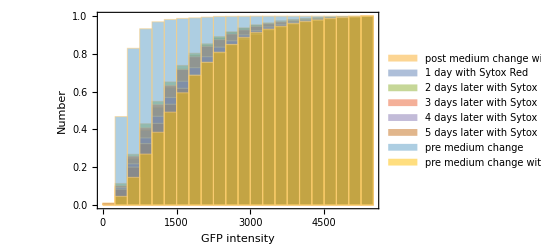
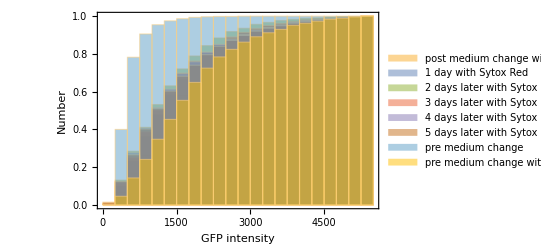
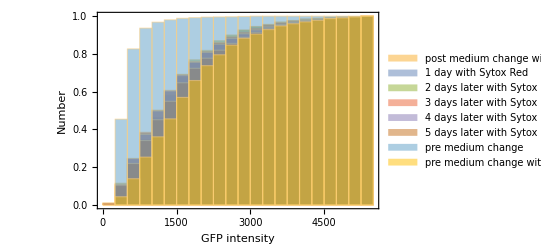
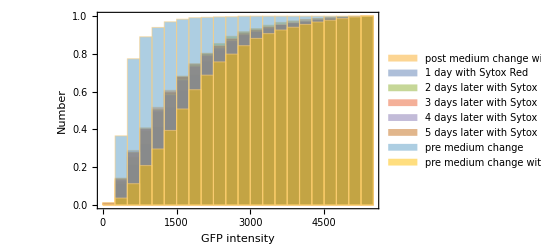

```mathematica
{Histogram[Table[gfpIntensitiesWell1[[i]],{i,Length[gfpIntensitiesWell1]}], {0,5500,250},"CDF",Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}],
Histogram[Table[gfpIntensitiesWell2[[i]],{i,Length[gfpIntensitiesWell2]}],  {0,5500,250},"CDF",Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}],
Histogram[Table[gfpIntensitiesWell3[[i]],{i,Length[gfpIntensitiesWell3]}],  {0,5500,250},"CDF",Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}],
Histogram[Table[gfpIntensitiesWell4[[i]],{i,Length[gfpIntensitiesWell4]}], {0,5500,250}, "CDF",Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}],
Histogram[Table[gfpIntensitiesWell5[[i]],{i,Length[gfpIntensitiesWell5]}], {0,5500,250}, "CDF",Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}],Histogram[Table[gfpIntensitiesWell6[[i]],{i,Length[gfpIntensitiesWell6]}], {0,5500,250},"CDF",Frame->True, FrameLabel->{"GFP intensity","Number"}, ChartLegends->{"post medium change with Sytox Red", "1 day with Sytox Red", "2 days later with Sytox Red", "3 days later with Sytox Red", "4 days later with Sytox Red", "5 days later with Sytox Red", "pre medium change", "pre medium change with Sytox Red"}]}
```

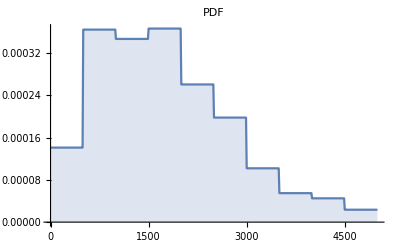
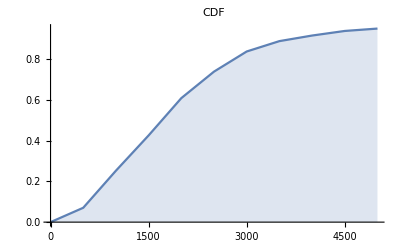
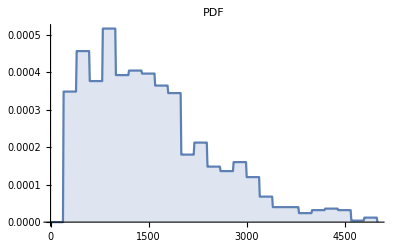
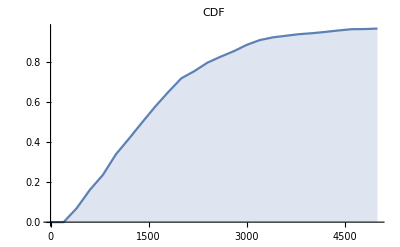
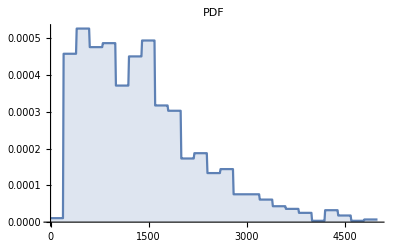
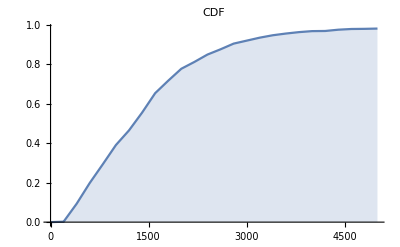
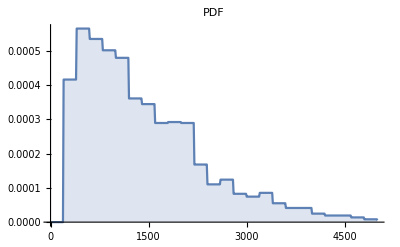
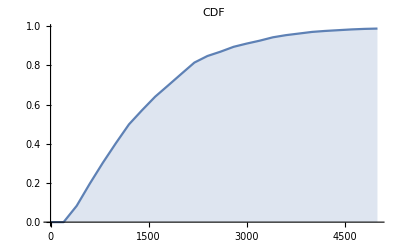

```mathematica
Table[
𝒟=HistogramDistribution[gfpIntensitiesWell1[[i]]];
DiscretePlot[#[𝒟,x],{x,0,5000,10},PlotLabel->#]&/@{PDF,CDF}, {i,Length[gfpIntensitiesWell1]}]
```

Absolute number and percentage of positive (> 1500) for post medium change with Sytox Red:

```mathematica
{Map[Function[gfpIntensity,Length[Select[gfpIntensity[[1]],#>1500&]]//N],{gfpIntensitiesWell1, gfpIntensitiesWell2, gfpIntensitiesWell3, gfpIntensitiesWell4, gfpIntensitiesWell5, gfpIntensitiesWell6}],Map[Function[gfpIntensity,Length[Select[gfpIntensity[[1]],#>1500&]]/Length[gfpIntensity[[1]]]//N],{gfpIntensitiesWell1, gfpIntensitiesWell2, gfpIntensitiesWell3, gfpIntensitiesWell4, gfpIntensitiesWell5, gfpIntensitiesWell6}]}
```

{{586.,1017.,2331.,874.,1182.,764.},{0.573947,0.62739,0.536602,0.54252,0.538742,0.60443}}

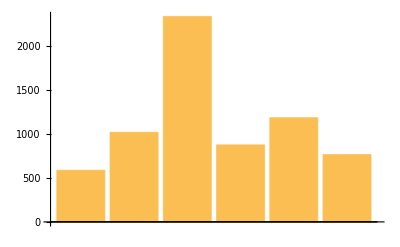

```mathematica
BarChart[{586.,1017.,2331.,874.,1182.,764.}]
```

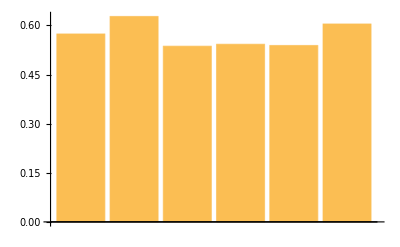

```mathematica
BarChart[{0.5739471106758081,0.6273904996915485,0.5366022099447514,0.54252017380509,0.5387420237010028,0.6044303797468354}]
```

Absolute number and percentage of positive (> 1000) for 1 day post medium change with Sytox Red:

```mathematica
{Map[Function[gfpIntensity,Length[Select[gfpIntensity[[2]],#>1500&]]//N],{gfpIntensitiesWell1, gfpIntensitiesWell2, gfpIntensitiesWell3, gfpIntensitiesWell4, gfpIntensitiesWell5, gfpIntensitiesWell6}],Map[Function[gfpIntensity,Length[Select[gfpIntensity[[2]],#>1500&]]/Length[gfpIntensity[[2]]]//N],{gfpIntensitiesWell1, gfpIntensitiesWell2, gfpIntensitiesWell3, gfpIntensitiesWell4, gfpIntensitiesWell5, gfpIntensitiesWell6}]}
```

{{572.,896.,1932.,802.,1096.,633.},{0.4576,0.479914,0.386168,0.431415,0.427457,0.497251}}

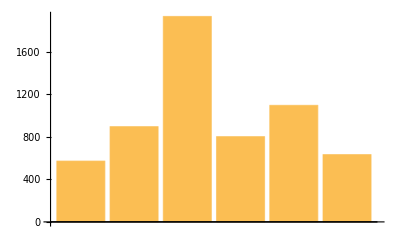

```mathematica
BarChart[{572.,896.,1932.,802.,1096.,633.}]
```

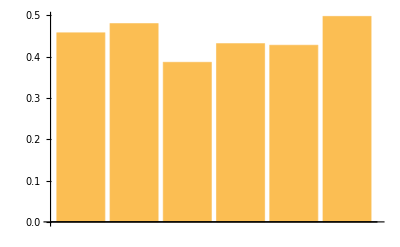

```mathematica
BarChart[{0.4576,0.4799143010176754,0.38616829902058764,0.4314147391070468,0.42745709828393136,0.49725058915946585}]
```

It looks like the absolute number stays pretty constant, whereas the percentage drops by about 10%.

### Viability

```mathematica
deadResultsDirectory="Z:\\results\\2017_12_15_expt_16\\2018_01_06_ilastik_dead_cell_results";
deadResultsFiles=FileNames["*.csv",deadResultsDirectory];
Map[FileNameTake,deadResultsFiles]//MatrixForm
```

(2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy1c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy2c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy3c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy4c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy5c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_1xy6c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy1c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy2c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy3c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy4c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy5c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytR_day_3xy6c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy1c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy2c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy3c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy4c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy5c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_post_medium_change_SytRxy6c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy1c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy2c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy3c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy4c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy5c4_table.csv
2018_01_06_ilastik_dead_cell_results-JC_171215_expt016_pre_medium_change_SytRxy6c4_table.csv)

```mathematica
deadResultsLists = Map[Import[#]&,deadResultsFiles];
```

Number of dead cells detected in each file, broken up into groups of time points:

```mathematica
Partition[deadResultsLists[[;;,-1,1]],6]
```

{{0,83,72,97,97,83},{0,117,141,140,109,33},{197,3099,1697,2497,3416,2007},{2428,5380,3158,4034,4142,3975}}

```mathematica
BarChart[Partition[deadResultsLists[[;;,-1,1]],6]]
```

-Graphics-